# Single microwave shielding adiabatic potentials

```mathematica
H={{Δ,Ω*Sin[ξ]/2, 0,Ω*Cos[ξ]/2},{Ω*Sin[ξ]/2,0,0,0},{0,0,0,0},{Ω*Cos[ξ]/2,0,0,0}}; (*/.{ξ->Pi/6, Ω->1,Δ->1};*)
```

```mathematica
H//MatrixForm
```

(Δ | 1/2 Ω Sin[ξ] | 0 | 1/2 Ω Cos[ξ]
1/2 Ω Sin[ξ] | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 Ω Cos[ξ] | 0 | 0 | 0)

```mathematica
H//TeXForm
```

\left(
\begin{array}{cccc}
 \Delta  & \frac{1}{2} \Omega  \sin (\xi ) & 0 & \frac{1}{2} \Omega  \cos (\xi ) \\
 \frac{1}{2} \Omega  \sin (\xi ) & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 \\
 \frac{1}{2} \Omega  \cos (\xi ) & 0 & 0 & 0 \\
\end{array}
\right)

```mathematica
Eigensystem[H]//FullSimplify
```

{{0,0,1/2 (Δ-√(Δ^2+Ω^2)),1/2 (Δ+√(Δ^2+Ω^2))},{{0,-Cot[ξ],0,1},{0,0,1,0},{((Δ-√(Δ^2+Ω^2)) Sec[ξ])/Ω,Tan[ξ],0,1},{((Δ+√(Δ^2+Ω^2)) Sec[ξ])/Ω,Tan[ξ],0,1}}}

```mathematica
(*-Sqrt[(1+Δ/Sqrt[Δ^2+Ω^2])/2]*)
```

```mathematica
(Δ+√(Δ^2+Ω^2))/Ω/Sqrt[((Δ+√(Δ^2+Ω^2))/Ω)^2+1]//FullSimplify
```

(Δ+√(Δ^2+Ω^2))/(Ω √(1+((Δ+√(Δ^2+Ω^2))^2)/Ω^2))

```mathematica
(Cot[t]+Csc[t])/Sqrt[(Cot[t]+Csc[t])^2+1]//FullSimplify
```

(Cot[t]+Csc[t])/(√(Csc[t/2]^2))

```mathematica
(Cos[t]+1)*Sin[t/2]/Sin[t]//FullSimplify
```

Cos[t/2]

```mathematica
u=Sqrt[(1+d/oe)/2];
v=Sqrt[(1-d/oe)/2];
u*v/.{oe->Sqrt[o^2+d^2]}//FullSimplify
```

1/2 √(o^2/(d^2+o^2))

```mathematica
mu={-Cos[x]/Sqrt[2]+Sin[x]/Sqrt[2], -I*Cos[x]/Sqrt[2]-I*Sin[x]/Sqrt[2]};
muC={-Cos[x]/Sqrt[2]+Sin[x]/Sqrt[2], I*Cos[x]/Sqrt[2]+I*Sin[x]/Sqrt[2]};
r={Cos[p]*Sin[t],Sin[p]*Sin[t]};
```

```mathematica
(*Magnitude of induced dipole moment*)
```

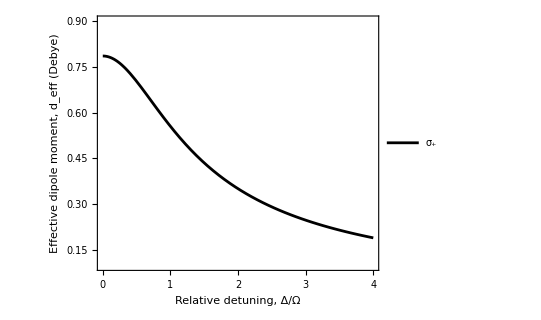

```mathematica
Plot[{2.72/Sqrt[12*(1 + Subscript[δ, r]^2)]},{Subscript[δ, r],0,4},PlotRange->{0.1,0.9},PlotStyle->{Black},PlotLegends->{"σ_+","π"},Frame->True,FrameLabel->{Style["Relative detuning, Δ/Ω",FontSize->16],Style["Effective dipole moment, d_eff (Debye)",FontSize->15]},AspectRatio->0.8]
```

```mathematica
S=(mu*Exp[-I*w*time]+muC*Exp[I*w*time]).r//FullSimplify
```

√2 Sin[t] (-Cos[p-time w] Cos[x]+Cos[p+time w] Sin[x])

```mathematica
Integrate[S^2/(2Pi/w),{time,0,2Pi/w}]//FullSimplify
```

Sin[t]^2 (1-Cos[2 p] Sin[2 x])

```mathematica
(mu*Exp[-I*w*time]+muC*Exp[I*w*time]).(mu*Exp[-I*w*time]+muC*Exp[I*w*time])//FullSimplify
```

2-2 Cos[2 time w] Sin[2 x]

```mathematica
3Cos[t]^2-1+3*Sin[2x]*Sin[t]^2*Cos[2p]/.{x->Pi/4}//FullSimplify
```

-1+3 Cos[t]^2+3 Cos[2 p] Sin[t]^2

```mathematica
(*Two-molecule matrix elements*)
```

```mathematica
$Assumptions={Element[u,Reals], Element[v,Reals],Element[ϵ,Reals],Element[θ, Reals], Element[ϕ,Reals]};
Off[ClebschGordan::phy](*suppress CG warnings*)
Off[ClebschGordan::tri] (*sppress CG warnings*)
```

```mathematica
PlusState={u,v*Sin[ϵ],0,v*Cos[ϵ]};
MinusState={-v,u*Sin[ϵ],0,u*Cos[ϵ]};
ZeroState={0,0,1,0};
XiMinusState={0,Cos[ϵ],0,-Sin[ϵ]};
quantumNumbers={{0,0},{1,-1},{1,0},{1,1}};
dPlus=quantumNumbers[[4]];
dMinus=quantumNumbers[[2]];
dZero=quantumNumbers[[3]];
Σ20={{dPlus,dMinus},{dMinus,dPlus},{dZero,dZero},{dZero,dZero}};
Σ2p1={{dPlus,dZero},{dZero,dPlus}};
Σ2m1={{dMinus,dZero},{dZero,dMinus}};
Σ2p2={{dPlus,dPlus}};
Σ2m2={{dMinus,dMinus}};
S1={{PlusState,PlusState}};
S2={{ZeroState,PlusState},{PlusState,ZeroState}};
S3={{PlusState,XiMinusState},{XiMinusState,PlusState}};
S4={{PlusState,MinusState},{MinusState,PlusState}};
S5={{MinusState,ZeroState},{ZeroState,MinusState}};
S6={{MinusState,XiMinusState},{XiMinusState,MinusState}};
S7={{MinusState,MinusState}};
basis={S1,S2,S3,S4,S5,S6,S7};
```

```mathematica
SphericalHarmony[q3_,q2_,q1_]:=Sqrt[(2q1[[1]]+1)*(2q2[[1]]+1)/(4Pi*(2q3[[1]]+1))]*ClebschGordan[{q1[[1]],0},{q2[[1]],0},{q3[[1]],0}]*ClebschGordan[{q1[[1]],q1[[2]]},{q2[[1]],q2[[2]]},{q3[[1]],q3[[2]]}];
LimitTotalJFinal[qn1_,qn2_]:=Boole[qn1[[1]]+qn2[[1]]<2];
InnerProd[braComponents1_,braComponents2_,op1_,op2_,ketComponents1_,ketComponents2_]:=
Sum[Sum[LimitTotalJFinal[quantumNumbers[[i]],quantumNumbers[[k]]]*LimitTotalJFinal[quantumNumbers[[j]],quantumNumbers[[l]]]*braComponents1[[i]]*ketComponents1[[j]]*SphericalHarmony[quantumNumbers[[i]],op1,quantumNumbers[[j]]],{i,1,4},{j,1,4}]*
braComponents2[[k]]*ketComponents2[[l]]*SphericalHarmony[quantumNumbers[[k]],op2,quantumNumbers[[l]]],{k,1,4},{l,1,4}];
MatrixElement[op_,bra_,ket_]:=
(1/Sqrt[Dimensions[bra][[1]]])*(1/Sqrt[Dimensions[ket][[1]]])*
Sum[
Sum[InnerProd[bra[[b]][[1]],bra[[b]][[2]],op[[i]][[1]],op[[i]][[2]],ket[[k]][[1]],ket[[k]][[2]]],{i,1,Dimensions[op][[1]]}],{b,1,Dimensions[bra][[1]]},{k,1,Dimensions[ket][[1]]}]//FullSimplify;
```

```mathematica
Σ20Matrix=Table[4*Pi*MatrixElement[Σ20,basis[[r]],basis[[c]]],{r,1,Dimensions[basis][[1]]},{c,1,Dimensions[basis][[1]]}];
Σ2p1Matrix=Table[4*Pi*MatrixElement[Σ2p1,basis[[r]],basis[[c]]],{r,1,Dimensions[basis][[1]]},{c,1,Dimensions[basis][[1]]}];
Σ2m1Matrix=Table[4*Pi*MatrixElement[Σ2m1,basis[[r]],basis[[c]]],{r,1,Dimensions[basis][[1]]},{c,1,Dimensions[basis][[1]]}];
Σ2p2Matrix=Table[4*Pi*MatrixElement[Σ2p2,basis[[r]],basis[[c]]],{r,1,Dimensions[basis][[1]]},{c,1,Dimensions[basis][[1]]}];
Σ2m2Matrix=Table[4*Pi*MatrixElement[Σ2m2,basis[[r]],basis[[c]]],{r,1,Dimensions[basis][[1]]},{c,1,Dimensions[basis][[1]]}];
Σ20Final=Σ20Matrix/(4Pi Sqrt[6]);
Σ2p1Final=Σ2p1Matrix/(4Pi Sqrt[2]);
Σ2m1Final=Σ2m1Matrix/(4Pi Sqrt[2]);
Σ2p2Final=Σ2p2Matrix/(4Pi);
Σ2m2Final=Σ2m2Matrix/(4Pi);
Σ2List={Σ2m2Final, Σ2m1Final,Σ20Final, Σ2p1Final,Σ2p2Final };
```

```mathematica
(*Bare hamiltonian without dipole-dipole interaction*)
```

```mathematica
Hin[δ_,Ωeff_]:=DiagonalMatrix[{0,-(δ+Ωeff)/2,-(δ+Ωeff)/2,-Ωeff,-(δ+3Ωeff)/2,-(δ+3Ωeff)/2,-2Ωeff}];
```

```mathematica
(*Everything together*)
```

```mathematica
HDD[r_,d_, δ_,Ω_, θ_,ϕ_,ξ_]:=Hin[δ,Sqrt[δ^2+Ω^2]]-8*Sqrt[2/15]*Pi^(3/2)*d*(1/r^3)*Sum[Conjugate[SphericalHarmonicY[2,m-3,θ,ϕ]]*Σ2List[[m]],{m,1,5}]/.{ϵ->ξ,u->Sqrt[(1+δ/Sqrt[δ^2+Ω^2])/2],v->Sqrt[(1-δ/Sqrt[δ^2+Ω^2])/2]};
```

```mathematica
DD=7.53; (*MHz, coupling constant, with lenths measured in units of 1000a0*);
CentrifugalTerm=0.0; (*MHz*)
CVdW6=3399*10^-6; (*MHz*)
θCollision={0,Pi/2,Pi/2};
ϕCollision={0,0,Pi/2};
δMW=30 (*MHz*);
ΩR=50(*MHz*);
ξMW=0*π/180;
ClassicalTurningPointValue=(500*10^-9)*(1.381*10^-23)/(10^6*6.626*10^-34) ;
```

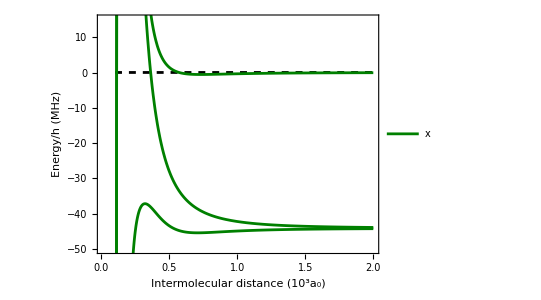

```mathematica
(*Adiabatic potential curves*)
zCollisionAdiabats=Eigenvalues[HDD[r,DD,δMW,ΩR,θCollision[[1]],ϕCollision[[1]],ξMW]]-CVdW6/r^6;
xCollisionAdiabats=Eigenvalues[HDD[r,DD,δMW,ΩR,θCollision[[2]],ϕCollision[[2]],ξMW]]-CVdW6/r^6;
yCollisionAdiabats=Eigenvalues[HDD[r,DD,δMW,ΩR,θCollision[[3]],ϕCollision[[3]],ξMW]]-CVdW6/r^6;
zCollisions=Plot[Evaluate@Table[zCollisionAdiabats[[i]],{i,1,7}],{r,0.1,2},PlotStyle->Lighter[Red,0.25],PlotLegends->{"z"},Frame->True];
xCollisions=Plot[Evaluate@Table[xCollisionAdiabats[[i]],{i,1,7}],{r,0.1,2}, PlotStyle->Darker[Green,0.5],PlotLegends->{"x"},Frame->True];
yCollisions=Plot[Evaluate@Table[yCollisionAdiabats[[i]],{i,1,7}],{r,0.1,2},PlotStyle->Lighter[Blue,0.5],PlotLegends->{"y"},Frame->True];
ClassicalTurningPoint=Plot[ClassicalTurningPointValue,{r,0.1,2},PlotStyle->{Black,Dashed,Thick},Frame->True];
Show[{ClassicalTurningPoint,xCollisions (*,yCollisions , xCollisions *)},
PlotRange->{{0.01,2},{-50,15}},FrameLabel->{{ Style["Energy/h (MHz)",16],None},{Style["Intermolecular distance (10^3a_0)",16],
Style["δ = 2π x " <>ToString@δMW <> " MHz, " <> "Ω = 2π x " <> ToString@ΩR <> " MHz, " <> "ξ = " <> ToString[ξMW*180/Pi,InputForm] <> "°", 16]}},AspectRatio->0.75]
```

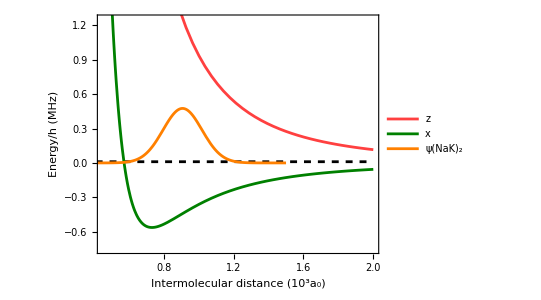

```mathematica
(*Showing field-linked bound states might appear even with perfectly circular polarization*)
zCollisions=Plot[Evaluate@Table[zCollisionAdiabats[[i]],{i,1,7}],{r,0.25,2},PlotStyle->Lighter[Red,0.25],PlotLegends->{"z"},Frame->True];
xCollisions=Plot[Evaluate@Table[xCollisionAdiabats[[i]],{i,1,7}],{r,0.25,2}, PlotStyle->Darker[Green,0.5],PlotLegends->{"x"},Frame->True];
yCollisions=Plot[Evaluate@Table[yCollisionAdiabats[[i]],{i,1,7}],{r,0.25,2},PlotStyle->Lighter[Blue,0.5],PlotLegends->{"y"},Frame->True];
ClassicalTurningPoint=Plot[ClassicalTurningPointValue,{r,0.25,2},PlotStyle->{Black,Dashed,Thick},Frame->True];
FakeWfn=Plot[Sqrt[r]*Exp[-(r-0.90)^2/0.025]/2,{r,0.25,1.5},PlotRange->Full,PlotStyle->{Orange},Frame->True,PlotLegends->{"ψ(NaK)_2"}];
Show[{ClassicalTurningPoint,zCollisions,xCollisions,FakeWfn (*, xCollisions, zCollisions*)},
PlotRange->{{0.45, 2.0},{-0.75,1.25}},
FrameLabel->{{ Style["Energy/h (MHz)",16],None},{Style["Intermolecular distance (10^3a_0)",16],
Style["δ = 2π x " <>ToString@δMW <> " MHz, " <> "Ω = 2π x " <> ToString@ΩR <> " MHz, " <> "ξ = " <> ToString[ξMW*180/Pi,InputForm] <> "°", 16]}},AspectRatio->0.75]
```

```mathematica
(*Reduced two-body Hamiltonian by projecting into S1, S2, S3*)
H123Subspace=Hin[δ,Sqrt[δ^2+Ω^2]]-8*Sqrt[2/15]*Pi^(3/2)*d*(1/r^3)*Sum[Conjugate[SphericalHarmonicY[2,m-3,θ,ϕ]]*Σ2List[[m]],{m,1,5}];
H123Subspace=H123Subspace[[1;;3,1;;3]]/.{ϵ->0};
```

```mathematica
H123Subspace//FullSimplify//MatrixForm
```

((d u^2 v^2 (1+3 Cos[2 θ]))/(6 r^3) | (d ⅇ^(-ⅈ ϕ) u^2 v Cos[θ] Sin[θ])/r^3 | (d ⅇ^(-2 ⅈ ϕ) u^2 v Sin[θ]^2)/(√2 r^3)
(d ⅇ^(ⅈ ϕ) u^2 v Cos[θ] Sin[θ])/r^3 | (2 d u^2-3 r^3 (δ+√(δ^2+Ω^2))-6 d u^2 Cos[θ]^2)/(6 r^3) | -(d ⅇ^(-ⅈ ϕ) u^2 Cos[θ] Sin[θ])/(√2 r^3)
(d ⅇ^(2 ⅈ ϕ) u^2 v Sin[θ]^2)/(√2 r^3) | -(d ⅇ^(ⅈ ϕ) u^2 Cos[θ] Sin[θ])/(√2 r^3) | -(d u^2+3 r^3 (δ+√(δ^2+Ω^2))-3 d u^2 Cos[θ]^2)/(6 r^3))

```mathematica
U2={{1,0,0},
{0,Sqrt[2/(Cos[θ]^2+1)]*Cos[θ],-Sqrt[1/(Cos[θ]^2+1)]*Sin[θ]*Exp[-I*ϕ]},
{0,Sqrt[1/(Cos[θ]^2+1)]*Sin[θ]*Exp[I*ϕ],Sqrt[2/(Cos[θ]^2+1)]*Cos[θ]}};
```

```mathematica
H123SubspaceBlock=ConjugateTranspose[U2].H123Subspace.U2/.{d/r^3->Κ,√(δ^2+Ω^2)->Ωef};//FullSimplify
```

```mathematica
H123SubspaceBlock//FullSimplify//MatrixForm
```

(1/6 u^2 v^2 Κ (1+3 Cos[2 θ]) | 1/2 ⅇ^(-ⅈ ϕ) u^2 v Κ √(3+Cos[2 θ]) Sin[θ] | 0
1/2 ⅇ^(ⅈ ϕ) u^2 v Κ √(3+Cos[2 θ]) Sin[θ] | 1/12 (-6 δ-5 u^2 Κ-6 Ωef-3 u^2 Κ Cos[2 θ]) | 0
0 | 0 | 1/6 (-3 δ+2 u^2 Κ-3 Ωef))

```mathematica
H123Eigs=Eigenvalues[H123SubspaceBlock[[1;;2,1;;2]]]//FullSimplify
```

{1/24 (-6 δ+u^2 (-5+2 v^2) Κ-6 Ωef+3 u^2 (-1+2 v^2) Κ Cos[2 θ]-ⅇ^(-2 ⅈ ϕ) √(ⅇ^(4 ⅈ ϕ) ((6 δ+u^2 (5-2 v^2) Κ+6 Ωef+3 u^2 (1-2 v^2) Κ Cos[2 θ])^2+16 u^2 v^2 Κ (3 δ+16 u^2 Κ+3 Ωef+9 (δ+Ωef) Cos[2 θ])))),1/24 ⅇ^(-2 ⅈ ϕ) (-ⅇ^(2 ⅈ ϕ) (6 δ+u^2 (5-2 v^2) Κ+6 Ωef+3 u^2 (1-2 v^2) Κ Cos[2 θ])+√(ⅇ^(4 ⅈ ϕ) ((6 δ+u^2 (5-2 v^2) Κ+6 Ωef+3 u^2 (1-2 v^2) Κ Cos[2 θ])^2+16 u^2 v^2 Κ (3 δ+16 u^2 Κ+3 Ωef+9 (δ+Ωef) Cos[2 θ]))))}

```mathematica
(*Effective potentials*)
```

```mathematica
Veff
```

# Dual microwave shielding, simple calculations

```mathematica
Clear[Hdouble]
Hdouble[ws_,wp_,dp_,ds_]:={{0,Sin[f]ws/2, wp/2,Cos[f]ws/2},
{Sin[f]ws/2,-ds,0,0},
{wp/2,0,-dp,0},
{Cos[f]ws/2,0,0,-ds}}/.{f->0*Pi/180};
```

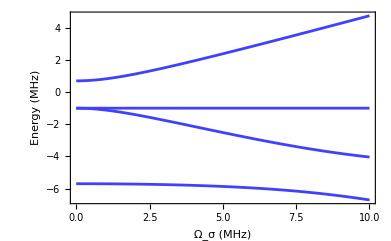

```mathematica
p=Plot[Evaluate@Table[Eigenvalues[Hdouble[ws,4,5,1]][[i]],{i,1,4}],{ws,0.0,10},PlotStyle->Lighter[Blue,0.25],Frame->True,FrameLabel->{Style["Ω_σ (MHz)",FontSize->14],Style["Energy (MHz)", FontSize->14],Style["Double MW dressing, Δ_π = 5 MHz, Ω_π = 4 MHz, Δ_σ = 1 MHz", FontSize->14]}];
txt=Graphics[{Text[Style["|0,0>",FontSize->14],{0.5,0.7}],
Text[Style["|1,m>",FontSize->14],{0.5,-2.7}],
Text[Style["|+>",FontSize->14],{6.5,1.7}],
Text[Style["|0>, |ξ_->",FontSize->14],{6.5,-1.5}],
Text[Style["|->",FontSize->14],{6.5,-3.7}]}];
Show[p]
```

```mathematica
(*INDUCED/EFFECTIVE DIPOLE MOMENT*)
```

```mathematica
dEffCalc1[Ωσ_,Ωπ_,δσ_,δπ_]:=Module[{Hdouble,evals,evecs,UpUp,dπ,dσ},
Hdouble={{0,0, Subscript[Ω, π]/2,Subscript[Ω, σ]/2},
{0,-Subscript[Δ, σ],0,0},
{Subscript[Ω, π]/2,0,-Subscript[Δ, π],0},
{Subscript[Ω, σ]/2,0,0,-Subscript[Δ, σ]}}/.{Subscript[Ω, σ]->Ωσ,Subscript[Ω, π]->Ωπ,Subscript[Δ, π]->δπ,Subscript[Δ, σ]->δσ};
{evals,evecs}=Eigensystem[Hdouble];
UpUp=evecs[[Ordering[N[evals],-1][[1]]]];(*Take eigenstate with the highest eigenvalue*)
UpUp=UpUp/Norm[UpUp];
dσ=2*UpUp[[1]]*UpUp[[4]]/Sqrt[12];
dπ=2*UpUp[[1]]*UpUp[[3]]/Sqrt[6];
Return[2.72*Sqrt[Abs[dσ^2 - dπ^2]]]
]
```

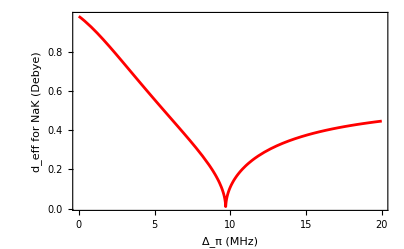

```mathematica
Plot[dEffCalc1[7.9,6.5,8,deltaPi],{deltaPi,0,20},PlotRange->Full,PlotStyle->Red,Frame->True,
FrameLabel->{Style["Δ_π (MHz)",FontSize->16], Style["d_eff for NaK (Debye)", FontSize->16],Style["Ω_σ = 7.9 MHz, Δ_σ = 8 MHz, Ω_π = 6.5 MHz",FontSize->16]}]
```

```mathematica
(*DIPOLAR LENGTH*)
```

```mathematica
adip[Ωσ_,Ωπ_,δσ_,δπ_]:=Module[{Hdouble,evals,evecs,UpUp,adip},
Hdouble={{0,0, Subscript[Ω, π]/2,Subscript[Ω, σ]/2},
{0,-Subscript[Δ, σ],0,0},
{Subscript[Ω, π]/2,0,-Subscript[Δ, π],0},
{Subscript[Ω, σ]/2,0,0,-Subscript[Δ, σ]}}/.{Subscript[Ω, σ]->Ωσ,Subscript[Ω, π]->Ωπ,Subscript[Δ, π]->δπ,Subscript[Δ, σ]->δσ};
{evals,evecs}=Eigensystem[Hdouble];
UpUp=evecs[[Ordering[N[evals],-1][[1]]]];(*Take eigenstate with the highest eigenvalue*)
UpUp=UpUp/Norm[UpUp];
adip=17.77*2.72^2*Abs[UpUp[[1]]]^2 * (2 * Abs[UpUp[[3]]]^2 - Abs[UpUp[[4]]]^2)/3;(*44.01 magic factor, 5.53 for NaCs D=4.75*)
Return[adip]
]
```

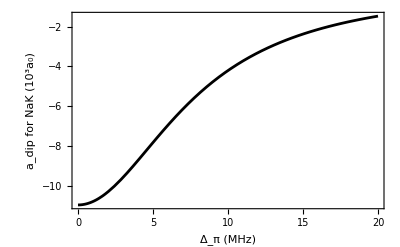

```mathematica
Plot[adip[7.9,0,deltaSigma,5],{deltaSigma,0,20},PlotRange->Full,PlotStyle->Black,Frame->True,
FrameLabel->{Style["Δ_π (MHz)",FontSize->16], Style["a_dip for NaK (10^3a_0)", FontSize->16],Style["Ω_σ = 7.9 MHz, Δ_σ = 8 MHz, Ω_π = 6.5 MHz",FontSize->16]}]
```

```mathematica
(*Effective potential, following Tao Shi 2025*)
```

```mathematica
VDoubleEff[r_,θ_,wSigma_,wPi_,dSigma_,dPi_]:=Module[{Hdouble,C3,C6,η,a,b,c,o,w0,w1,w2,evals,evecs,E0,Em1,Em,Ep},
Hdouble={{0,wSigma/2, wPi/2,0},
{wSigma/2,-dSigma,0,0},
{wPi/2,0,-dPi,0},
{0,0,0,-dSigma}};
{evals,evecs}=Eigensystem[Hdouble];
UpUp=evecs[[Ordering[N[evals],-1][[1]]]];(*Take eigenstate with the highest eigenvalue*)
UpUp=UpUp/Norm[UpUp];
PiState=If[dSigma>=dPi,evecs[[Ordering[N[evals],-2][[1]]]],evecs[[Ordering[N[evals],-4][[1]]]]];
PiState=PiState/Norm[PiState];
Ep=evals[[Ordering[N[evals],-1][[1]]]];
Em1=-dSigma;
E0=If[dSigma<dPi,evals[[Ordering[N[evals],-4][[1]]]],evals[[Ordering[N[evals],-2][[1]]]]];;
Em=If[dSigma>=dPi,evals[[Ordering[N[evals],-2][[1]]]],evals[[Ordering[N[evals],-4][[1]]]]];
a=ArcCos[UpUp[[1]]];
b=ArcCos[UpUp[[2]]/Sin[a]];
c=ArcSin[PiState[[1]]/Sin[a]];
o=0.001;
η=Sqrt[8Pi/15];(*d^2/e0*)
w0=-1/(288Pi^2);
w0=w0*((Sin[a]^2*(3Cos[a]^2Sin[2b]Cos[c]+(1/2)(Cos[a]+Cos[3a])(3Cos[2b]-1)Sin[c])^2)/(E0-Ep)
+(Cos[a]^2Sin[a]^2(Cos[2a](1-3Cos[2b])Cos[c]+3Cos[a]Sin[2b]Sin[c])^2)/(Em-Ep)
+(Sin[a]^4Cos[a]^2Sin[c]^2(3Sin[2b]Cos[c]+Cos[a](3Cos[2b]-1)Sin[c])^2)/(E0-Ep)
+(Sin[a]^4Cos[a]^2(3Sin[2b]Cos[2c]+Cos[a](3Cos[2b]-1)Sin[2c])^2)/(E0+Em-2Ep)
+(Sin[a]^4Cos[a]^4Cos[c]^4(1-3Cos[2b]+3Sec[a]Sin[2b]Tan[c])^2)/(Em-Ep));
w1=(Sin[a]^2Cos[a]^4Sin[b]^2)/((4Pi^2)*(Ep-Em1-o))
+(Sin[a]^4Cos[a]^2Sin[b]^2Cos[c]^2)/((4Pi^2)*(2Ep-Em-Em1-o))
+(Sin[a]^4Cos[a]^2Sin[b]^2Sin[c]^2)/((4Pi^2)*(2Ep-E0-Em1-o))
+(Sin[a]^4Cos[a]^2Cos[b]^2Cos[c]^2*(Cos[a]Sin[b]Cos[c]+Cos[b]Sin[c])^2)/((2Pi^2)*(2Ep-2Em+o))
+(Sin[a]^4Cos[a]^2Sin[b]^2Sin[c]^2*(Sin[b]Cos[c]+Cos[a]Cos[b]Sin[c])^2)/((2Pi^2)*(2Ep-2E0-o))
+(Sin[a]^4Cos[a]^2Sin[b]^2Cos[c]^2*(Cos[a]Cos[b]Cos[c]-Sin[b]Sin[c])^2)/((2Pi^2)*(2Ep-2Em-o))
+(Sin[a]^4Cos[a]^2Cos[b]^2Sin[c]^2*(Cos[b]Cos[c]-Cos[a]Sin[b]Sin[c])^2)/((2Pi^2)*(2Ep-2E0+o))
+(Sin[a]^2Cos[a]^2Cos[b]^2*(Cos[2a]Sin[b]Cos[c]+Cos[a]Cos[b]Sin[c])^2)/((4Pi^2)*(Ep-Em+o))
+(Sin[a]^2Cos[a]^2Sin[b]^2*(Cos[2a]Cos[b]Sin[c]+Cos[a]Sin[b]Cos[c])^2)/((4Pi^2)*(Ep-E0-o))
+(Sin[a]^2Cos[a]^2Sin[b]^2*(Cos[2a]Cos[b]Cos[c]-Cos[a]Sin[b]Sin[c])^2)/((4Pi^2)*(Ep-Em-o))
+(Sin[a]^4Cos[a]^2Sin[b]^2*(Sin[b]Cos[2c]+Cos[a]Cos[b]Sin[2c])^2)/((4Pi^2)*(2Ep-E0-Em-o))
+(Sin[a]^2Cos[a]^2Cos[b]^2*(Cos[2a]Sin[b]Sin[c]-Cos[a]Cos[b]Cos[c])^2)/((4Pi^2)*(Ep-E0+o))
+(Sin[a]^4Cos[a]^2Cos[b]^2*(Cos[a]Sin[b]Sin[2c]-Cos[2c]Cos[b])^2)/((4Pi^2)*(2Ep-E0-Em+o));
w2=1/(8Pi^2);
w2=w2*((Cos[a]^4Cos[b]^2Sin[a]^2)/(Ep-Em1)
+(Sin[a]^4Cos[a]^2Cos[b]^2Cos[c]^2)/(2Ep-Em-Em1)
+(Sin[a]^4Cos[a]^2Cos[b]^2Sin[c]^2)/(2Ep-E0-Em1));
C3=Sqrt[15/(2Pi)]*(η/(48Pi))*(3*Cos[2*b]-1)*Cos[a]^2*Sin[a]^2;
C6=15*η^2*w2/(32Pi);
Return[(C3/r^3)*(3Cos[θ]^2-1) + (C6/r^6)*(Sin[θ]^4+(w1/w2)*Sin[θ]^2Cos[θ]^2+(w0/w2)*(3Cos[θ]^2-1)^2)]
]
```

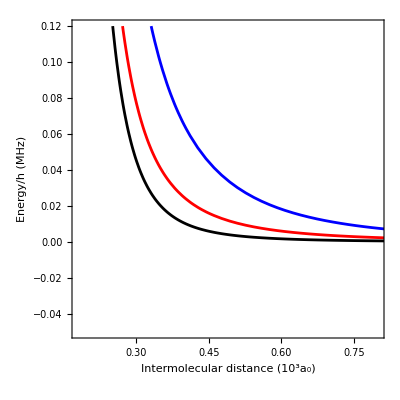

```mathematica
Plot[{VDoubleEff[r,0,7.9,4.0,8,10],
VDoubleEff[r,0,7.9,5.9,8,10],
VDoubleEff[r,0,7.9,6.5,8,10]},{r,0.2,1},PlotRange->{{0.18,0.8},{-0.05,0.12}},PlotStyle->{Blue,Red,Black},Frame->True,FrameLabel->{
Style["Intermolecular distance (10^3a_0)",16], Style["Energy/h (MHz)",16],Style["θ = 0, Ω_σ = 7.9 MHz, Δ_σ = 8 MHz, Ω_π = 6.5 MHz",FontSize->14]},(*PlotLegends->{"Ω_π = 4.0 MHz","Ω_π = 5.9 MHz","Ω_π = 6.5 MHz"},*)AspectRatio->1]
```

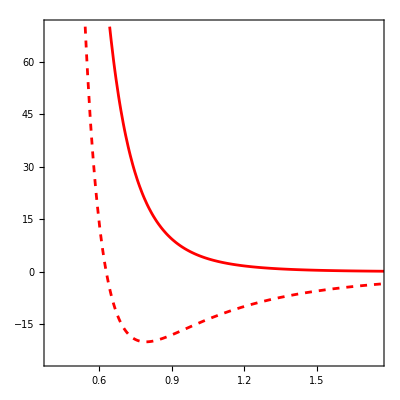

```mathematica
Plot[{5/r^6,5/r^6 -20/r^3},{r,0.1,2},PlotStyle->{{Red},{Red,Dashed}},PlotRange->{{0.4,1.75},{-25,70}},Frame->True,FrameTicks->None,AspectRatio->1]
```